# Initial conditions

```mathematica
(*we keep the same values for unrescaled quantities as the numerical solution notebook for matching*)
```

```mathematica
m1N=1.5;m2N=1;G=1; (*cN=1;*) cN = 1/(√ϵ);  ϵ=0.001   ; (* tfin = 10;*)
spinSuppressFac = 0.001 ; 

MN = m1N+m2N ;  μN = m1N m2N/MN ;

M = m1+m2 ;  μ = m1 m2/M ;
δ1=2 m1 m2/M^2 (1+3/4 m2/m1)  ;   δ2=2 m2 m1/M^2 (1+3/4 m1/m2) ;
δ1N=2 m1N m2N/MN^2 (1+3/4 m2N/m1N)  ;δ2N=2 m2N m1N/MN^2 (1+3/4 m1N/m2N) ;

Rinit={0.1,0.3,0}; 
Pinit={-1,1,1};   
S1init={0,1,1}spinSuppressFac;
S2init={1,-0.3,0}spinSuppressFac;


S1ninit = Norm[S1init];
S2ninit = Norm[S2init];
rinit=Rinit/(G MN)     ;
pinit=Pinit/μN ;
Linit=Cross[rinit,pinit] ;
Lninit = Norm[Linit] ;
(*Prepare  a sign function for later use in solution*)

If [ δ2N/(cN^2 Norm[rinit]^3 S1ninit Lninit)Linit.Cross[S1init, S2init]   > 0, sign =1, sign =-1 ] ;
```

# unrescaled quantities

```mathematica
R = {Rx, Ry,Rz} ; P ={Px,Py,Pz};
S1= {S1x, S1y,S1z} ;    S2= {S2x, S2y,S2z} ;
S1n = Norm[S1] ;     S2n = Norm[S2] ;
Seff= δ1 S1+ δ2 S2;
Enwt=(P.P)/(2 μ) -(G μ M)/Norm[R];(*Newtonian expression for energy*)
Lun=Norm[Cross[R,P]];  (*norm of unscaled ang momentum*)
kGoldstein = G M μ ;
e = (1 + 2 Enwt  Lun^2/(μ kGoldstein^2))^(1/2) ;

(*Newtonian eccentricity in unrescaled variables*)
aUnrescaled= -kGoldstein/(2 Enwt) ;
a = aUnrescaled/(G M) ;
```

# scaled quantities

```mathematica
r=R/(G M);       p=P/μ;
L=Cross[r,p] ;

(*Conserved quantities defined in terms of scaled variables*) 

Ln=Norm[L] ;
Jn=Norm[L+S1+S2];
SeffL= Seff.L ;
```

```mathematica
σ1=(S1.S2)/(S1n S2n) -Ln/S2n(δ1-δ2)/δ2(S1.L)/(Ln S1n) ;   (*σ1=Cos γ -L/S2(Q1-Q2)/Q2 Cos κ1 *)
σ2= (S2.L)/(Ln S2n) + (δ1 S1n)/(δ2 S2n)(S1.L)/(Ln S1n) ;           (*σ2= Cos κ2 +(Q1 S1)/(Q2 S2) Cos κ1*)

(*Evaluating σ1 and σ2*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;
m1 = m1N ; m2 = m2N ;

σ1N=(S1.S2)/(S1n S2n) -Ln/S2n(δ1-δ2)/δ2(S1.L)/(Ln S1n) ;
σ2N=(S2.L)/(Ln S2n) + (δ1 S1n)/(δ2 S2n)(S1.L)/(Ln S1n) ;

Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
```

# cubic equation

```mathematica
A=2 Ln S1n δ1 (δ2-δ1);cubiceq=x^3 -(Ln^2 (δ1-δ2)^2+2 δ2 Ln σ2 S2n  (δ2-δ1)+S1n^2 δ1^2+2 δ1 δ2 σ1 S1n S2n +δ2^2  S2n^2  )x^2/A+ (2  δ2 S2n (Ln σ1(δ2-δ1) +σ2( δ1 S1n+ δ2 σ1 S2n) )) x/A+-S2n^2 δ2^2 (σ1^2+σ2^2-1)1/A;(*=(x -x1)(x -x2)(x -x3)*)
```

```mathematica
(*evaluate the cubic and find the roots*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;
m1 = m1N ; m2 = m2N ;

rtsol=Solve[cubiceq==0,x] ;
x2N=x/.rtsol[[1]] ; 
x3N=x/.rtsol[[2]] ;
x1N=x/.rtsol[[3]];
{x2N, x3N, x1N} = Sort[{x2N, x3N, x1N}] ;
Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
```

# solution of Cosκ1

```mathematica
βe = e/(1+(1-e^2)^(1/2)) ;
ν = u + 2 ArcTan[ (βe Sin[u])/(1-βe Cos[u])]      ;(*same as ν= 2 ArcTan[√((1+e)/(1-e)) Tan[u/2]] but without the ArcTan issues*)

β = ((x3-x2)/(x1-x2))^(1/2);
α =  sign 2/(√(A(x1-x2)))EllipticF[ArcSin[√(((S1init.Linit)/(Lninit S1ninit)-x2)/(x3-x2))],β^2]   ;
Υ = 1/2 √(A(x1-x2))(α+(ν + e Sin[ν])/(c^2 Ln^3)) ;
coskp1=x2+(x3-x2)JacobiSN[Υ,β^2]^2;
```

```mathematica
(*Evaluate coskp1*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;
m1 = m1N ; m2 = m2N ; 
x1=x1N;x2=x2N;x3=x3N;
c=cN;


(*n = (Ln/(a (1-e^2)^(1/2)))^3  ;
usol =FindRoot[n tfin == u - e Sin[u],{u,10000}]
coskp1/.usol

Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
*)
```

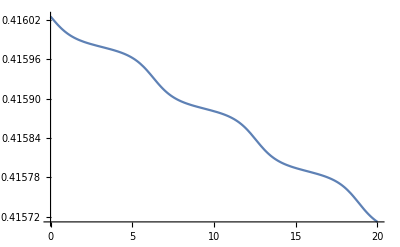

```mathematica
n = (Ln/(a (1-e^2)^(1/2)))^3  ;
Plot[coskp1,{u,0,20}]     (*just  a check*)
```

```mathematica
fr[λ_?NumericQ]:=FindRoot[n λ == u - e Sin[u],{u,0}];
(*func[time_] :=  u/.fr[time]
Plot[func[time],{time,0,2}]*)
```

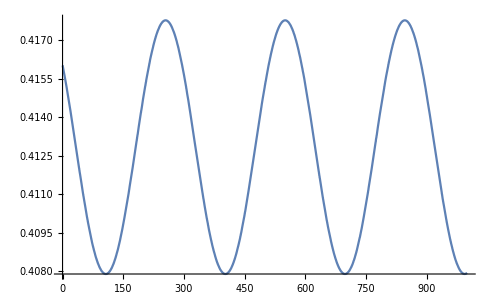
```mathematica
fcoskp1[λ_?NumericQ]:=coskp1/.fr[λ];
fcoskp1num=  -Graphics- ;  (* imported from 1.5PN_hamiltonian_flow_numerical_1PN_terms_ignored.nb*)
Show[Plot[fcoskp1[λ],{λ,0,1000},PlotStyle->Red],fcoskp1num, PlotRange->All]

(*Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
*)
```

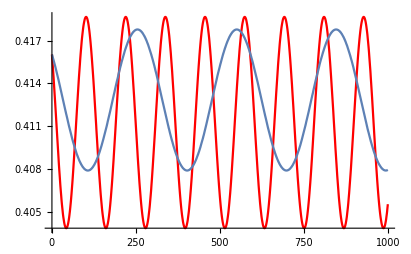

```mathematica
Quit[];
```